```mathematica
(*WHITE DWARF ELECTRON*)
```

```mathematica
R=7*10^6;(*in m*)
```

```mathematica
vesc=6*10^6;(*in m/sec*)
vbar=20*10^3;(*in m/sec*)
```

```mathematica
mr[mx_?NumericQ]:=(mn *mx)/(mn+mx);
δp[mx_?NumericQ]:=2^0.5*mr[mx]*vesc*1.78*10^-27;
hbar=(6.626*10^-34)/(2*3.14);
pf=hbar*(3*π^2*n)^(1/3);
```

```mathematica
ρx=10^6*10^3;(*in GeV/m^3*)(*Due to Overdensity*)
```

```mathematica
mn=0.5*10^-3;(*in GeV*)
```

```mathematica
t=3 10^17(*Age in sec*);
n=10^36;(*in m^-3*)
Nn=4/3*π *R^3*n;
sigmasat=(π*R^2)/Nn;
```

```mathematica
G=6.67*10^-11;(*in SI*)
ρ=10^11;(*in kg/m^3*)
```

```mathematica
kb=1.38*10^-23;(*in J/k*)
```

```mathematica
rth[mx_,T_]:=((9*kb*T)/(4*π*G*ρ*mx*1.78*10^-27))^0.5;
```

```mathematica
vth[mx_,T_]:=4/3*π*rth[mx,T]^3;
asq[mx_]:=3/2*vesc^2/vbar^2*(4*mx*mn)/(mx-mn)^2;
b[mx_,sigmadmdm_]:=(ρx/mx*(6/π)^0.5*sigmadmdm*vbar*(vesc^2/vbar^2-2/3));
a[mx_,sigma_]:=(ρx/mx*(6/π)^0.5*Min[sigma,sigmasat]*Min[1,δp[mx]/pf]*vbar*Nn*vesc^2/vbar^2*(1-(1-Exp[-asq[mx]])/asq[mx]));
```

```mathematica
teq[mx_,sigma_,sigmadmdm_,T_,anncross_]:=2/((b[mx,sigmadmdm]^2+4*a[mx,sigma]*anncross/vth[mx,T])^0.5);
teq[100,sigmasat,100/(5.62*10^27),10^7,3*10^-32]
```

4.27634×10^7

```mathematica
ldm[mx_,sigma_,sigmadmdm_,T_,anncross_]:=mx*(a[mx,sigma]+b[mx,sigmadmdm]*(b[mx,sigmadmdm]+(b[mx,sigmadmdm]^2+4*a[mx,sigma]*anncross/vth[mx,T])^0.5)/(2*anncross/vth[mx,T]));
```

```mathematica
ldm[100,10^-43,100/(5.62*10^27),10^7,3*10^(3-2)];
```

```mathematica
myticks={{Automatic,None},{{{-2,"10^-2"},{0,"1"},{2,"10^2"},{4,"10^4"},{6,"10^6"},{8,"10^8"}},None}};
```

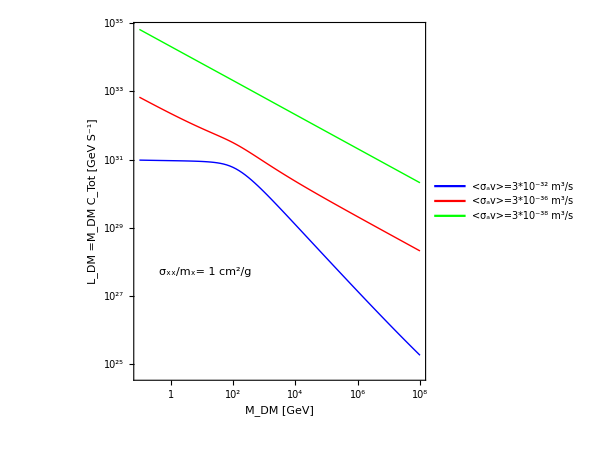

```mathematica
ListLogPlot[{Table[{x,ldm[10^x,sigmasat,10^x/(5.62*10^27),10^7,3*10^-32]},{x,-1,8,0.1}],Table[{x,ldm[10^x,sigmasat,10^x/(5.62*10^27),10^7,3*10^-36]},{x,-1,8,0.1}],Table[{x,ldm[10^x,sigmasat,10^x/(5.62*10^27),10^7,3*10^-38]},{x,-1,8,0.1}]},Joined-> True,PlotStyle->{{Thick,Blue},{Thick,Red},{Thick,Green}},Frame->True,FrameStyle->Directive[14, "Times",Black],AxesOrigin->{-1,Automatic},FrameTicks->myticks,PlotLegends->Placed[{"<σ_av>=3*10^-32 m^3/s","<σ_av>=3*10^-36 m^3/s","<σ_av>=3*10^-38 m^3/s"},{0.8,0.9}],Epilog->Style[Text["σ_xx/m_x= 1 cm^2/g",Log@{3.0,0.5*10^28}],15],FrameLabel->{Style[" M_DM [GeV]",FontSize->20,Bold,FontFamily->"Times New Roman"],Style["L_DM\ =M_DM \ C_Tot [GeV S^-1]",FontSize->20,Bold,FontFamily->"Times New Roman"]},AspectRatio->1,ImageSize->450]
```

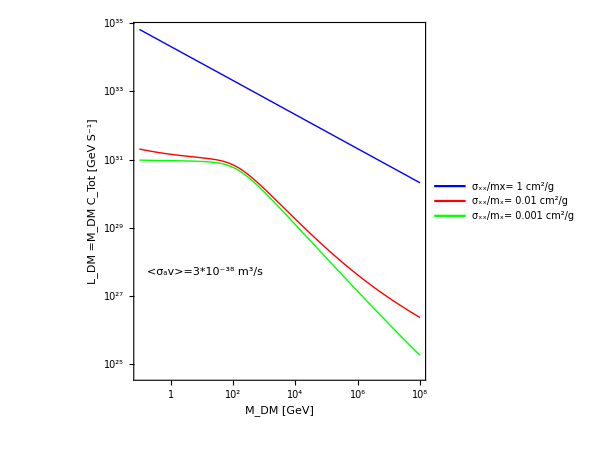

```mathematica
ListLogPlot[{Table[{x,ldm[10^x,sigmasat,10^x/(5.62*10^27),10^7,3*10^-38]},{x,-1,8,0.1}],Table[{x,ldm[10^x,sigmasat,(0.01*10^x)/(5.62*10^27),10^7,3*10^-38]},{x,-1,8,0.1}],Table[{x,ldm[10^x,sigmasat,(0.001*10^x)/(5.62*10^27),10^7,3*10^-38]},{x,-1,8,0.1}]},Joined-> True,PlotStyle->{{Thick,Blue},{Thick,Red},{Thick,Green}},Frame->True,FrameStyle->Directive[14, "Times",Black],AxesOrigin->{-1,Automatic},FrameTicks->myticks,PlotLegends->Placed[{"σ_xx/mx= 1 cm^2/g","σ_xx/m_x= 0.01 cm^2/g","σ_xx/m_x= 0.001 cm^2/g"},{0.8,0.85}],Epilog->Style[Text["<σ_av>=3*10^-38 m^3/s",Log@{3.0,0.5*10^28}],15],FrameLabel->{Style[" M_DM [GeV]",FontSize->20,Bold,FontFamily->"Times New Roman"],Style["L_DM\ =M_DM \ C_Tot [GeV S^-1]",FontSize->20,Bold,FontFamily->"Times New Roman"]},AspectRatio->1,ImageSize->450]
```

```mathematica
anncross=3*10^-32;(*in m^3/sec*)
mx=10^3;
```

```mathematica
mx*a[mx,sigmasat]
```

1.09528×10^30

```mathematica
mx*b[mx,mx/(5.62*10^27)]*(b[mx,mx/(5.62*10^27)]+(b[mx,mx/(5.62*10^27)]^2+4*a[mx,sigmasat]*anncross/vth[mx,10^7])^0.5)/(2*anncross/vth[mx,10^7])
```

2.71565×10^28

```mathematica
anncross=3*10^-41;(*in m^3/sec*)
mx=10^-2;
```

```mathematica
mx*a[mx,sigmasat]
```

8.43735×10^30

```mathematica
mx*b[mx,mx/(5.62*10^27)]*(b[mx,mx/(5.62*10^27)]+(b[mx,mx/(5.62*10^27)]^2+4*a[mx,sigmasat]*anncross/vth[mx,10^7])^0.5)/(2*anncross/vth[mx,10^7])
```

2.0777×10^38

```mathematica
(*when the annihilation cross section is low then the self capture term is dominating but for thermal relic cross section (annihilation cross section is not so low) ordinary capture is dominating*)
```

```mathematica
(*WHITE DWARF ELECTRON*)
```

```mathematica
R=5.77*10^6;(*in m*)
```

```mathematica
vesc=6*10^6;(*in m/sec*)
vbar=20*10^3;(*in m/sec*)
```

```mathematica
mr[mx_?NumericQ]:=(mn *mx)/(mn+mx);
δp[mx_?NumericQ]:=2^0.5*mr[mx]*vesc*1.78*10^-27;
hbar=(6.626*10^-34)/(2*3.14);
pf=hbar*(3*π^2*n)^(1/3);
```

```mathematica
ρx=10^6*10^3;(*in GeV/m^3*)(*Due to Overdensity*)
```

```mathematica
mn=0.5*10^-3;(*in GeV*)
```

```mathematica
t=3 10^17(*Age in sec*);
n=10^36;(*in m^-3*)
Nn=4/3*π *R^3*n;
sigmasat=(π*R^2)/Nn;
```

```mathematica
G=6.67*10^-11;(*in SI*)
ρ=10^11;(*in kg/m^3*)
```

```mathematica
kb=1.38*10^-23;(*in J/k*)
```

```mathematica
rth[mx_,T_]:=((9*kb*T)/(4*π*G*ρ*mx*1.78*10^-27))^0.5;
```

```mathematica
vth[mx_,T_]:=4/3*π*rth[mx,T]^3;
asq[mx_]:=3/2*vesc^2/vbar^2*(4*mx*mn)/(mx-mn)^2;
b[mx_,sigmadmdm_]:=(ρx/mx*(6/π)^0.5*sigmadmdm*vbar*(vesc^2/vbar^2-2/3));
a[mx_,sigma_]:=(ρx/mx*(6/π)^0.5*Min[sigma,sigmasat]*Min[1,δp[mx]/pf]*vbar*Nn*vesc^2/vbar^2*(1-(1-Exp[-asq[mx]])/asq[mx]));
```

```mathematica
teq[mx_,sigma_,sigmadmdm_,T_,anncross_]:=2/((b[mx,sigmadmdm]^2+4*a[mx,sigma]*anncross/vth[mx,T])^0.5);
```

```mathematica
ldm[mx_,sigma_,sigmadmdm_,T_,anncross_]:=mx*(a[mx,sigma]+b[mx,sigmadmdm]*(b[mx,sigmadmdm]+(b[mx,sigmadmdm]^2+4*a[mx,sigma]*anncross/vth[mx,T])^0.5)/(2*anncross/vth[mx,T]));
```

```mathematica
(*ContourPlot[{ldm[10^x,0.0,10^y,10^7,10^-41]==2.05*10^31,10^y/10^x==1/(5.62*10^27)},{x,-3,6},{y,-20,-36},Frame->True,FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Thick,Blue},{Dashed,Red}},FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xx [m^2]",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500]*)
```

```mathematica
p=ContourPlot[{ldm[10^x,0.0,10^y,10^7,3*10^-38]==2.05*10^31},{x,-3,6},{y,-20,-36},Frame->True,FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Thick,Blue},{Dashed,Red}},FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xx [m^2]",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500];
```

General::munfl: Exp[-1.07522×10^6] is too small to represent as a normalized machine number; precision may be lost.

```mathematica
points=Catenate@Cases[Normal@p,Line[pts_]->pts,Infinity];
```

```mathematica
mchi=10^points[[All,1]];
sigmachi=10^points[[All,2]];
```

```mathematica
ratio=10^points[[All,2]]/10^points[[All,1]]*10^28/1.78;
```

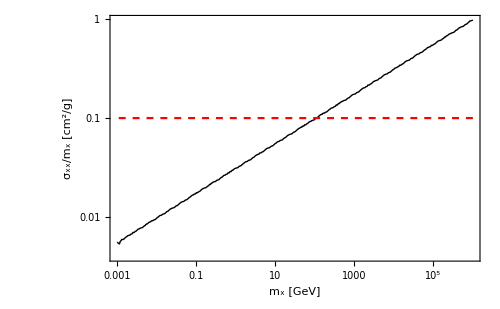

```mathematica
ListLogLogPlot[{Table[{mchi[[i]],ratio[[i]]},{i,Length[mchi]}],Table[{mchi[[i]],0.1},{i,Length[mchi]}]},PlotRange->All,Joined->True,PlotStyle->{{Thick,Black},{Dashed,Red}},Frame->True,AxesOrigin->{0.001,Automatic},FrameStyle->Directive[Black,16,FontFamily->"Times"],FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["σ_xx/m_x [cm^2/g]",FontSize->20,Bold]},ImageSize->500]
```

General::munfl: Exp[-1.07522×10^6] is too small to represent as a normalized machine number; precision may be lost.

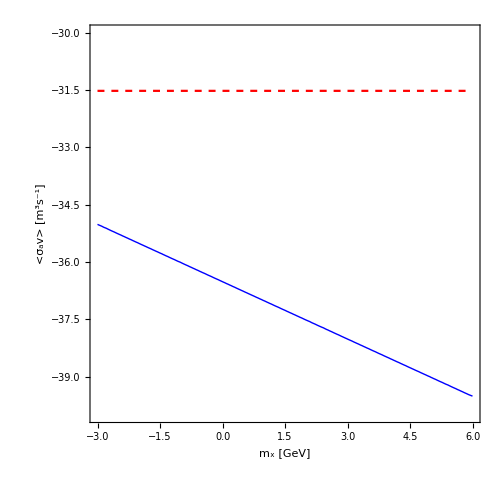

```mathematica
ContourPlot[{ldm[10^x,0.0,10^x/(5.62*10^28),10^7,10^y]==2.05*10^31,y==Log10[3*10^-32]},{x,-3,6},{y,-30,-40},Frame->True,FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Thick,Blue},{Dashed,Red}},FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["<σ_av> [m^3s^-1]",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500]
```

```mathematica
(*SUN ELECTRON*)
```

```mathematica
R=6.95*10^8;(*in m*)
```

```mathematica
vesc=618*10^3;(*in m/sec*)
vbar=287.5*10^3;(*in m/sec*)
```

```mathematica
mr[mx_?NumericQ]:=(mn *mx)/(mn+mx);
δp[mx_?NumericQ]:=2^0.5*mr[mx]*vesc*1.78*10^-27;
hbar=(6.626*10^-34)/(2*3.14);
pf=hbar*(3*π^2*n)^(1/3);
```

```mathematica
ρx=10^6*0.3;(*in GeV/m^3*)
```

```mathematica
mn=0.5*10^-3;(*in GeV*)
```

```mathematica
t=3 10^17(*Age in sec*);
n=10^30;(*in m^-3*)
Nn=4/3*π *R^3*n;
sigmasat=(π*R^2)/Nn;
```

```mathematica
G=6.67*10^-11;(*in SI*)
ρ=162.2*10^3;(*in kg/m^3*)
```

```mathematica
kb=1.38*10^-23;(*in J/k*)
```

```mathematica
rth[mx_,T_]:=((9*kb*T)/(4*π*G*ρ*mx*1.78*10^-27))^0.5;
```

```mathematica
vth[mx_,T_]:=4/3*π*rth[mx,T]^3;
asq[mx_]:=3/2*vesc^2/vbar^2*(4*mx*mn)/(mx-mn)^2;
b[mx_,sigmadmdm_]:=(ρx/mx*(6/π)^0.5*sigmadmdm*vbar*(vesc^2/vbar^2-2/3));
a[mx_,sigma_]:=(ρx/mx*(6/π)^0.5*Min[sigma,sigmasat]*Min[1,δp[mx]/pf]*vbar*Nn*vesc^2/vbar^2*(1-(1-Exp[-asq[mx]])/asq[mx]));
```

```mathematica
teq[mx_,sigma_,sigmadmdm_,T_,anncross_]:=2/((b[mx,sigmadmdm]^2+4*a[mx,sigma]*anncross/vth[mx,T])^0.5);
```

```mathematica
ldm[mx_,sigma_,sigmadmdm_,T_,anncross_]:=mx*(a[mx,sigma]+b[mx,sigmadmdm]*(b[mx,sigmadmdm]+(b[mx,sigmadmdm]^2+4*a[mx,sigma]*anncross/vth[mx,T])^0.5)/(2*anncross/vth[mx,T]));
```

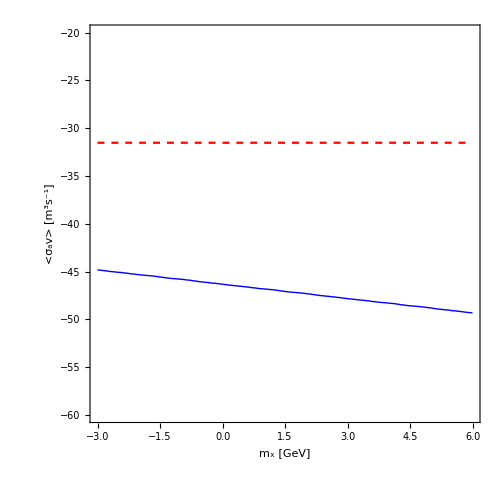

```mathematica
ContourPlot[{ldm[10^x,0.0,10^x/(5.62*10^28),10^7,10^y]==2.38*10^36,y==Log10[3*10^-32]},{x,-3,6},{y,-20,-60},Frame->True,FrameStyle->Directive[14, "Times",Black],ContourStyle->{{Thick,Blue},{Dashed,Red}},FrameLabel->{Style["m_x [GeV]",FontSize->20,Bold],Style["<σ_av> [m^3s^-1]",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500]
```